## §1 毕达哥拉斯定理

毕达哥拉斯三元数

满足a^2+b^2==c^2 的整数组(a,b,c)称为毕达哥拉斯三元数.

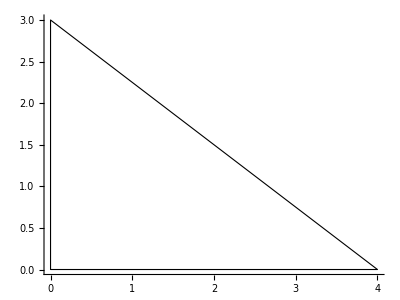

```mathematica
Graphics[{EdgeForm[Black],White,Triangle[{{0,0},{0,3},{4,0}}]},Axes->True]
```

生成毕达哥拉斯三元数的一般公式是
a=(p^2-q^2)r,b=2p q r,c=(p^2+q^2)r

```mathematica
(*习题1~2*)
a={119,3367,4601,12709,65,319,2291,799,481,4961,45,1679,161,1771,56};
c={169,4825,6649,18541,97,481,3541,1249,769,8161,75,2929,289,3229,106};
b=√(c^2-a^2)
Print["In list b which can't be divised by 60 are ",Select[b,Divisible[#,60]==False&]]
Print["In list b which can't be divised by 30 are ",Select[b,Divisible[#,30]==False&]]
Print["In list b which can't be divised by 12 are ",Select[b,Divisible[#,12]==False&]]
Clear["Global`*"]
```

{120,3456,4800,13500,72,360,2700,960,600,6480,60,2400,240,2700,90}

In list b which can't be divised by 60 are {3456,72,90}

In list b which can't be divised by 30 are {3456,72}

In list b which can't be divised by 12 are {90}

```mathematica
(*习题3*)
Print[Mod[1^2,4]," ",Mod[2^2,4]," ",Mod[3^2,4]]
Clear["Global`*"]
```

1 0 1

(*对于数n,假若它是偶数,则其平方被4除余0;
若果它是奇数,则其被4除可能余1,2,3;*)
n=p+r;(r=n mod 4)
n^2=(p+r)^2=p^2+2p r+r^2;
n^2 mod 4=r^2 mod 4;
r=1,2,3时,余数仅为0或1,证毕.

(*习题4*)
如果a, b同时为奇数, 则c为偶数.又由于c为偶数, 且c为完全平方数, 则c可以被4整除.但奇数的平方Mod4仅余1, 两奇数平方之和Mod4余2;故毕达哥拉斯三元数(a,b,c)中a,b不能同时为奇数.

丢番图问题

毕达哥拉斯三元数(a,b,c)可以导出边长为有理数(x=a/c,y=b/c,斜边为1)的直角三角形.所有这样的三角形的集合构成了一个单位圆.

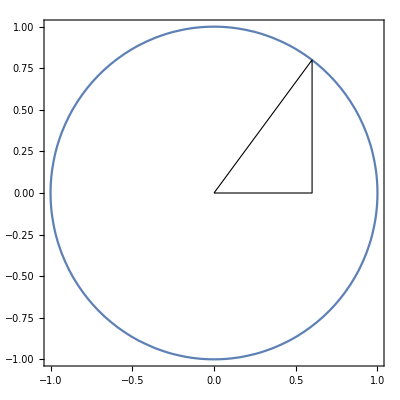

```mathematica
s1=ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Axes->True];
s2=Graphics[{EdgeForm[Black],White,Triangle[{{0,0},{3/5,4/5},{3/5,0}}]},Axes->True];
Show[{s1,s2}]
```

现在找出方程a^2+b^2==c^2 的整数解问题等价于找出方程x^2+y^2==1的有理数解问题,或者说是圆上的有理数点对.此类问题被称为丢番图问题.

(*习题1*)
对于毕达哥拉斯三元数(a,b,c)都有相应的(x,y)成立.而考虑弦-切线作图法,对相应的(x,y)可以表示为((1-t^2)/(1+t^2),(2t)/(1+t^2))其中t为有理数.设t=p/q,则有x=a/c=(p^2-q^2)/(p^2+q^2),y=b/c=(2pq)/(p^2+q^2).证毕.

(*习题2*)
由上题可知,对于没有公因子的(a,b,c)一般生成公式成立.
而对于有公因子的(a,b,c)则分子分母同乘上公因子.
既一般生成公式为欧几里得公式
a=r(p^2-q^2);b=r(2pq);c=r(p^2+q^2);
证毕.